# Multiple-fluid Force-free Current Sheet

## Setup

```mathematica
PacletDirectoryLoad["~/src/Beforerr.m"];
<<Beforerr`;
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
(* Change the directory to the current file location *)
SetDirectory@NotebookDirectory[];
SetOptions[safeSave,"Dir"->"../figures/"];

SaveP[suffix_:"",pp_,pJ_]:=Module[{},
safeSave["profiles"<>suffix,pp];
safeSave["J_profiles"<>suffix,pJ];
]
```

```mathematica
num=2;
```

## Equations and Rules

### Assumptions and Notation Rules

```mathematica
assums={B0≠0,δ1>0};
notationRules=Join[
{B0->Subscript[B, 0],Bx->Subscript[B, x],By->Subscript[B, y],Bz->Subscript[B, z]},
{Subscript[ui, i_]:>Subscript[u, i],Subscript[ni, i_]:>Subscript[n, i],Subscript[niInf, i_]:>Subscript[n, i][∞]},
{ux->Subscript[U, x],uy->Subscript[U, y],uu->U},
{Jx->Subscript[J, x],Jy->Subscript[J, y],Jxi->Subscript[J, x,i],Jyi->Subscript[J, y,i]},
{Γ1->Subscript[Γ, 1],Γe->Subscript[Γ, e],Λz->Subscript[Λ, z],Λy->Subscript[Λ, y]},
{vAInf->Subscript[V, A][∞],vAx->Subscript[V, A,x],vAy->Subscript[V, A,y]}
];
```

### First Equations

```mathematica
multiFluidConds={
Jx->Jxi+Jxe,Jy->Jyi+Jye,
Jxe->-(Γe Bx)/Bz,Jye->-(Γe By)/Bz,
ux->Jxi/n,uy->Jyi/n,uu->√(ux^2+uy^2),
Γe->Sum[Subscript[Γ, i],{i,num}],
n->Sum[Subscript[ni, i],{i,num}],
Γ1->(-Bz √Subscript[niInf, 1])/(√Sum[Subscript[λnInf, i] Subscript[λzInf, i]^2,{i,num}])
};
forceFreeConds={
Bx->B0 Cos[θ[z]],By->B0 Sin [θ[z]],
Jxi->nu Cos [θ[z]],Jyi->nu Sin[θ[z]]
};

uiRule=Subscript[ui, i_]:>(Subscript[Γ, i] B0)/(Subscript[niInf, i] Bz);
niRule[i_]:=Subscript[ni, i]->Subscript[Γ, i]/Γ1(Subscript[ni, 1]-Subscript[niInf, 1])+Subscript[niInf, i]
asymptoticConds=Join[
{uiRule},
Map[niRule,Range[2,num]]
];
ΓiRule:=Subscript[Γ, i_]:>Subscript[λnInf, i] Subscript[λzInf, i] Γ1
λnInfRule:=Subscript[λnInf, i_]:>Subscript[niInf, i]/Subscript[niInf, 1]
normalizeRules=Join[
{Bz->1,nInf->1},
{ΓiRule,λnInfRule}
];
```

```mathematica
eqθ:={θ'[z]==Bz/Γ1(Subscript[niInf, 1]-Subscript[ni, 1]),θ[0]==π/2};
s={Subscript[ni, 1]->Subscript[niInf, 1](1+c1/(1+(z/δ1 )^2))};
sol1=DSolve[eqθ/.s,θ[z],z]//First;
```

```mathematica
sol1/.notationRules
```

{θ[z]→(π Γ_1-2 c1 δ1 ArcTan[z/δ1] B_z n_1[∞])/(2 Γ_1)}

### Two-fluid Systems

```mathematica
twoFluidConds={Subscript[λzInf, 1]->1,Subscript[niInf, 2]->nInf-Subscript[niInf, 1]};
defs={vAInf->B0/√nInf,vAx->Bx/√n,vAy->By/√n};
conds=Join[multiFluidConds,asymptoticConds,forceFreeConds,twoFluidConds,normalizeRules,defs];
```

### Second Equations

```mathematica
ΛyBlock:={
eqUB:=(-Λy Subscript[ui, 1])/B0 Subscript[ni, 1]+Γe/Bz==-Bz/Γ1 Subscript[ni, 1]+B0/Subscript[ui, 1];
sol2=Solve[eqUB,Λy]//First;
Simplify[Λy/.sol2]
}
ΛyBlock/.notationRules
```

{(B_0 (-B_0 B_z Γ_1+u_1 (B_z^2 n_1+Γ_1 Γ_e)))/(B_z n_1 u_1^2 Γ_1)}

```mathematica
eqUB:=-nu/B0+Γe/Bz==-Bz/Γ1 Subscript[ni, 1]+B0/Subscript[ui, 1]
sol2=Solve[eqUB,nu ]//First;
Simplify[nu/.sol2]//.notationRules
```

B_0 (-B_0/u_1+(B_z n_1)/Γ_1+Γ_e/B_z)

```mathematica
sols=Join[s,sol1,sol2];
```

## Results

Because  every species also must satisfy the theta equations, we can get the equations to express n

```mathematica
profile={Bx,By,n,ux,uy};
jProfile={Jx,Jy,Jxi,Jyi};
profilePlot[profile_,rule_,zmax_]:=Plot[
Evaluate[profile//.Join[conds,sols,rule]],{z,-zmax,zmax},
PlotLegends->Evaluate[profile/.notationRules],AxesLabel->{"z",Automatic},
PlotRange->All
];
```

```mathematica
Manipulate[
Module[{tempRules,p1,p2},
tempRules={
B0->B0i,Subscript[λzInf, 2]->λzInfi,
Subscript[niInf, 1]->n1Inf,
c1->ci,δ1->δi
};
p1=profilePlot[profile,tempRules,zmaxi];
p2=profilePlot[jProfile,tempRules,zmaxi];
{p1,p2}
],
{{n1Inf,0.5} ,0,1},
{{λzInfi,-1} ,-2,0},
{{ci,1},0,2},
{{δi,1},1,10},
{{B0i,2},0.5,2},
{{zmaxi,10},5,30}
]
```

```mathematica
SaveP[suffix="_sym"]
```

File already exists

File already exists

## Examples

### Normalized velocity by Alfvén velocity

```mathematica
conf={ratio->0.5};
Bys=By//.Join[conds,sols];
exCond=(Bys/.z->∞)==ratio(Bys/.z->0)/.conf;
exCond=Simplify[exCond,assums];
condRule2=Solve[exCond,c1];
condRule2
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c1→-(2.0944 √niInf_1 √(1.-1. λzInf_2^2+λzInf_2^2/niInf_1))/(δ1 (-3.14159 niInf_1-3.14159 λzInf_2^2+3.14159 niInf_1 λzInf_2^2))},{c1→(2.0944 √niInf_1 √(1.-1. λzInf_2^2+λzInf_2^2/niInf_1))/(δ1 (-3.14159 niInf_1-3.14159 λzInf_2^2+3.14159 niInf_1 λzInf_2^2))}}

```mathematica
ratioList=Range[0.001,0.901,0.1];
ratioList=Range[0.001,0.501,0.1];
ratioLegend[r_]:="n_1="<>ToString[Round[r,0.1]]
legends=ratioLegend/@ratioList;
```

```mathematica
Manipulate[Module[{tempRules},
tempRules={
B0->B0i,Subscript[λzInf, 2]->λzInfi,
Subscript[niInf, 1]->n1Inf,
δ1->δi,First@First@ condRule2
};
p3=profilePlot[profile,tempRules,zmaxi];
p4=profilePlot[jProfile,tempRules,zmaxi];
{p3,p4}],
{{n1Inf,0.6} ,0,1},
{{λzInfi,-1} ,-2,0},
{{δi,1},1,10},
{{B0i,2},0.5,2},
{{zmaxi,10},5,30}
]
```

```mathematica
SaveP[suffix="_n1Inf=0.6",p3,p4]
```

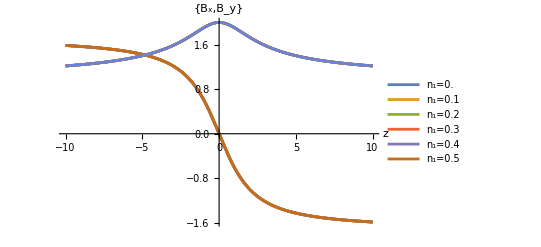
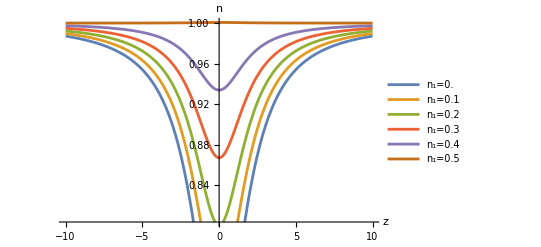
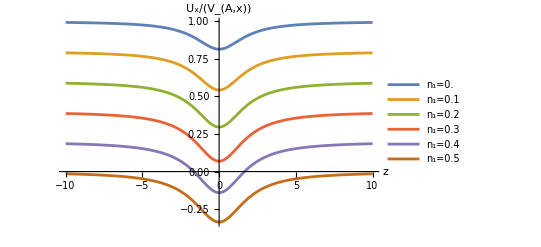
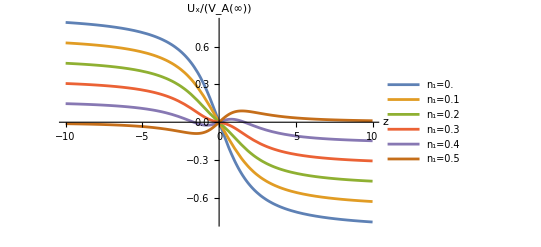
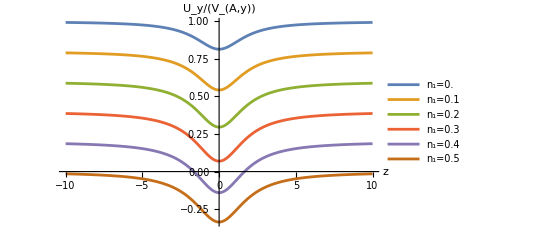
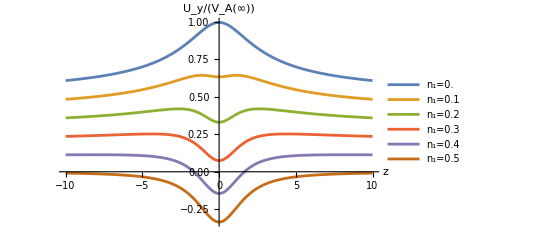

```mathematica
ps=Block[{zmax=10},
allRules=Join[ conds,sols,First@ condRule2,{Subscript[λzInf, 2]->-1,B0->2,δ1->2}];
exps={{Bx,By},n,ux/vAx, ux/vAInf,uy/vAy,uy/vAInf};
tempPlot[v_]:=Plot[
Evaluate[v//.allRules/.{Subscript[niInf, 1]->ratioList}],{z,-zmax,zmax},
PlotLegends->legends,AxesLabel->{"z",v/.notationRules}
];
tempPlot/@exps
]
```

```mathematica
safeSave["UxNormBx",ps[[3]]];
safeSave["UxNormB0",ps[[4]]];
safeSave["UyNormBy",ps[[5]]];
safeSave["UyNormB0",ps[[6]]];
```

### Asymptotic velocity

```mathematica
asymPlot[λzInfi_:-1,B0i_:2]:=Block[{δ1=1,z=∞},
allRules=Join[ conds,sols,First@ condRule2,{B0->B0i,Subscript[niInf, 1]->niInf1,Subscript[λzInf, 2]->λzInfi}];

exp={Abs@Subscript[ui, 1],Abs@Subscript[ui, 2],uu,uu/vAInf};
legends=exp/.notationRules;
tempExps=Simplify[exp//.allRules];
Plot[tempExps,{niInf1,0,1},
PlotLegends->legends,AxesLabel->{"n_1(∞)",None}]
]
```

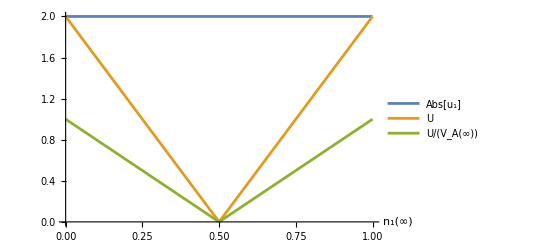

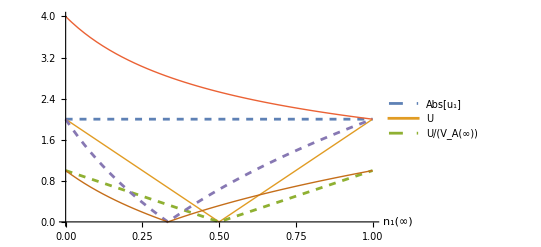

```mathematica
asymPlot[]
```

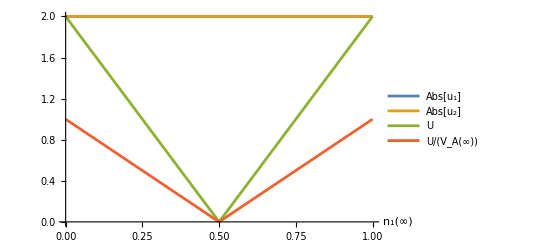

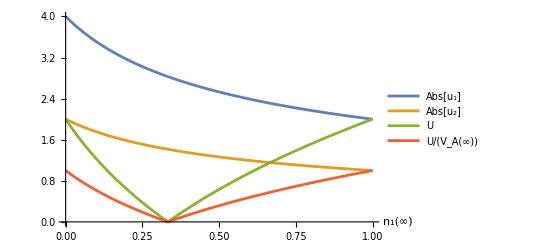

```mathematica
p1=asymPlot[]
p2=asymPlot[-1/2]
safeSave["vRatios",p1];
safeSave["vRatiosEx2",p2];
```

## Archive Codes

```mathematica
(*Define the system of equations*)
eq1:=D[Bx[z],z]==n1[z] u1y[z]+n2 u2y-GammaE By[z]/Bz;
eq2:=D[By[z],z]==-n1[z] u1x[z]-n2 u2x+GammaE Bx[z]/Bz;
eq3:=Gamma1 D[u1x[z],z]==n1[z] u1y[z] Bz-Gamma1 By[z];
eq4:=Gamma1 D[u1y[z],z]==Gamma1 Bx[z]-n1[z] u1x[z] Bz;
eq5:=D[(Gamma1^2/n1[z]+C1 n1[z]^γ/2),z]==n1[z] (u1x[z] By[z]-u1y[z] Bx[z]-Te/(2 ne) D[ne,z]);
ne:=n2+ n1[z];


u1xInf:=Gamma1 BxInf/(n1Inf Bz)
u1yInf:=Gamma1 ByInf/(n1Inf Bz)
bc1=Bx[zmin]==0;
bc2:=n1[zmax]==n1Inf+eps;
bc3:=Bx[zmax]==1-eps;
bc4:=By[zmax]==ByInf+eps;
bc6:=u1y[zmax]==u1yInf+eps;
bc5:=u1x[zmax]==u1xInf+eps;

BxInf=1;
γ=5/3;
zmax=10;
eps=0.01;
```

### Temperature

```mathematica
eqT:={Γ1^2/n1+1/2(n1 T1[z])==Γ1^2+1/2 T0};
```

## Another normalization

```mathematica
num=2;
eqAmJy:=Hold[D[Bx,z]]==Sum[Subscript[n, α] Subscript[uy, α],{α,num}]-ne uey
eqM1u[α_]:=Subscript[Γ, α] Hold@D[Subscript[ux, α],z]==Subscript[n, α] Subscript[uy, α] Bz - Subscript[Γ, α] By
forceFreeConds={
Bx->B0 Cos[θ[z]],
By->B0 Sin [θ[z]],
Subscript[uy, α_]:>Subscript[u, α] Sin[θ[z]],
Subscript[ux, α_]:>Subscript[u, α] Cos[θ[z]],
uey->(Γe By)/(ne Bz)
};
normRules={
Γe->Sum[Subscript[Γ, α],{α,num}],
Subscript[n, α_]:>Subscript[λ, α,n] Subscript[nInf, α],Subscript[nInf, α_]:>Subscript[C, α,n] Subscript[n, e,Inf],Subscript[u, α_]:>Subscript[C, α,u] Bz/(√Subscript[n, e,Inf]),
Subscript[Γ, α_]:>Subscript[nInf, α] Subscript[uzInf, α],Subscript[uzInf, α_]:>Subscript[C, α,uz] Bz/(√Subscript[n, e,Inf])
};
nRules={Subscript[n, e,Inf]->1,Bz->1};
Simplify[ReleaseHold[{eqAmJy,eqM1u[1]}//.forceFreeConds//.normRules/.nRules],Subscript[C, 1,n] !=0]
```

{Sin[θ[z]] (C_(1,n) (B0 C_(1,uz)-C_(1,u) λ_(1,n))+C_(2,n) (B0 C_(2,uz)-C_(2,u) λ_(2,n))-B0 θ'[z])==0,Sin[θ[z]] (C_(1,u) λ_(1,n)+C_(1,uz) (-B0+C_(1,u) θ'[z]))==0}

```mathematica
asymEq:=Bz^2==Sum[Subscript[Γ, α]^2/Subscript[nInf, α],{α,num}]
nEq:=1==Sum[Subscript[C, α,n],{α,num}]
(asymEq&&nEq)//.normRules/.nRules
```

1==C_(1,n) C_(1,uz)^2+C_(2,n) C_(2,uz)^2&&1==C_(1,n)+C_(2,n)

```mathematica
eqTwoθ:=(Subscript[C, 1,n] Subscript[C, 1,u] Subscript[λ, 1,n]+Subscript[C, 2,n] Subscript[C, 2,u] Subscript[λ, 2,n]-B0 Γe)/B0==(Subscript[C, 1,u] Subscript[λ, 1,n]-Subscript[C, 1,uz] B0)/(Subscript[C, 1,u] Subscript[C, 1,uz])
λ2sol=First@Solve[eqTwoθ//.normRules/.nRules,Subscript[λ, 2,n]]
```

{λ_(2,n)→(-B0^2 C_(1,uz)+B0 C_(1,n) C_(1,u) C_(1,uz)^2+B0 C_(1,u) C_(1,uz) C_(2,n) C_(2,uz)+B0 C_(1,u) λ_(1,n)-C_(1,n) C_(1,u)^2 C_(1,uz) λ_(1,n))/(C_(1,u) C_(1,uz) C_(2,n) C_(2,u))}

```mathematica
asymConds={
Subscript[C, 1,u]->Subscript[C, 1,uz] B0,
Subscript[C, 2,u]->Subscript[C, 2,uz] B0
};
eqθ:={Subscript[C, 1,u] Subscript[λ, 1,n]+Subscript[C, 1,uz] (-B0+Subscript[C, 1,u] θ'[z])==0,θ[0]==π/2}
s={Subscript[λ, 1,n]->1+c/(1+z^2)};
sol=First@DSolve[eqθ/.asymConds/.s,θ[z],z]
```

{θ[z]→(-2 c ArcTan[z]+π C_(1,uz))/(2 C_(1,uz))}

```mathematica
eqRules={
nTotal->Sum[Subscript[n, α] ,{α,num}]
};
rules=Join[forceFreeConds,normRules,nRules,asymConds,sol,λ2sol,eqRules];
```

```mathematica
{Bx,nTotal}//.rules//.temprule/.s
```

{B0 Cos[1/2 (π-2 c ArcTan[z])],0.6 (1+c/(1+z^2))-(-0.8 B0^2+0.4 B0^2 (1+c/(1+z^2)))/B0^2}

{Bx,By,nTotal,ux,uy}

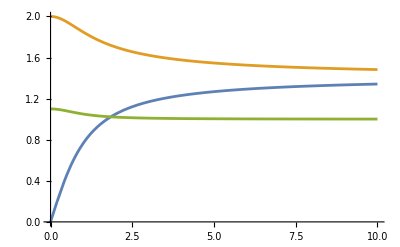

```mathematica
profile={Bx,By,nTotal,ux,uy}
Block[{B0=2,c=0.5,c1=0.6},
temprule={Subscript[C, 1,n]->c1,Subscript[C, 2,n]->1-Subscript[C, 1,n],Subscript[C, 1,uz]->1,Subscript[C, 2,uz]->-1};
Plot[Evaluate[profile//.rules//.temprule/.s],{z,0,10},PlotRange->All]
]
```

## MHD

```mathematica
Vx[z_]:=V0 Cos[φ[z]]
Vy[z_]:=V0 Sin[φ[z]]
Bx[z]:=B0 Cos[φ[z]]
By[z]:=B0 Sin[φ[z]]

V:={Vx[z],Vy[z],Vz[z]};
B:={Bx[z],By[z],Bz};
r={x,y,z};
J:=Curl[B,r]
(*J:={Jx,Jy,Jz}*)
eqM:=Γ  D[V,z]+Grad[p[z],r]==J×B
eqM
```

{-V0 Γ Sin[φ[z]] φ'[z],V0 Γ Cos[φ[z]] φ'[z],p'[z]+Γ Vz'[z]}=={-B0 Bz Sin[φ[z]] φ'[z],B0 Bz Cos[φ[z]] φ'[z],0}

```mathematica
eqM1:=-V0 Γ Sin[φ[z]] φ'[z]==-B0 Bz Sin[φ[z]] φ'[z]//Simplify
eqM2:=V0 Γ Cos[φ[z]] φ'[z]==B0 Bz Cos[φ[z]] φ'[z]//Simplify
{eqM1,eqM2}
```

{(B0 Bz-V0 Γ) Sin[φ[z]] φ'[z]==0,(B0 Bz-V0 Γ) Cos[φ[z]] φ'[z]==0}